# 3.2 : Stability exponents for a toy model

#### a)

The limit cycle in this question corresponds to a zero of the r equation:

```mathematica
Solve[μ*r-r^3==0,r]
```

{{r→0},{r→-√μ},{r→√μ}}

Since we assume r >= 0 and r = 0 is a fixed point (not a limit cycle), there is only 1 limit cycle at r0 = sqrt(μ).
The angular velocity is then given by dθ/dt = ω + ν r0^2 = ω + ν μ, such that the period becomes: T = 2π/(dθ/dt) = 2π/(ω+ν μ)

#### b)

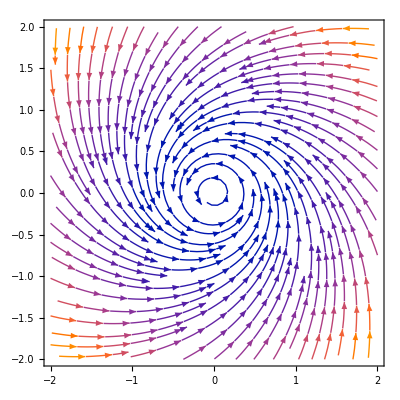

```mathematica
StreamPlot[{x/10-y^3-x*y^2-x^2*y-y-x^3, x+y/10+x*y^2+x^3-y^3-x^2*y}, {x,-2,2}, {y,-2,2}]
```

It’s constructive to quickly look at the fixed point and determine its behaviour/stability. This will help us understand the flow and how to plot it better.

```mathematica
Solve[{x/10-y^3-x*y^2-x^2*y-y-x^3==0, x+y/10+x*y^2+x^3-y^3-x^2*y==0},{x,y}]
```

{{x→0,y→0}}

Only 1 fixed point at the origin, which turns out to be an unstable spiral, which can be deduced from the Jaccobian A:

```mathematica
A = {{1/10,-1},{1,1/10}};
```

```mathematica
Eigenvalues[A]
```

{1/10+ⅈ,1/10-ⅈ}

Since the eigenvalues are complex with positive real part, we are dealing with an unstable spiral, so trajectories move away from the origin.

```mathematica
sol2[x0_ , y0_] :=NDSolve[
{x'[t]== x[t]/10-y[t]^3-x[t]*y[t]^2-x[t]^2*y[t]-y[t]-x[t]^3, 
y'[t] == x[t]+y[t]/10+x[t]*y[t]^2+x[t]^3-y[t]^3-x[t]^2*y[t], x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,10}]
```

```mathematica
dz = 0.5;
```

```mathematica
z =1.5;
```

```mathematica
initialC=Tuples[{Range[-z,z,dz],Range[-z,z,dz]}];
```

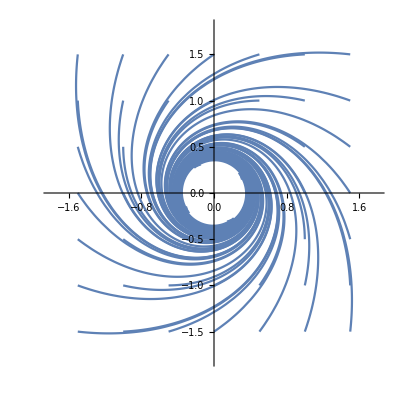

```mathematica
p2 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol2[initialC[[i,1]] , initialC[[i,2]]]]
,{t,0,6} , PlotRange->{{-1.8,1.8} , {-1.8,1.8}}],
{i,1,Length[initialC]}]/. Line[x_] :> {Arrowheads[{0.03,0.0,0.03,0.0,0.03,0.03}], Arrow[x]}]
```

We also use some initial conditions near the origin (within the limit cycle):

```mathematica
initialC2={{0.1,0.1}, {0.2,-0.15}};
```

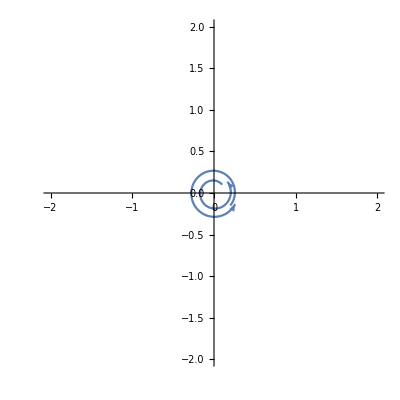

```mathematica
p4 = Show[
Table[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol2[initialC2[[i,1]] , initialC2[[i,2]]]]
,{t,0,6} , PlotRange->{{-2,2} , {-2,2}}],
{i,1,Length[initialC2]}]/. Line[x_] :> {Arrowheads[{0.03,0.0,0.03,0.0,0.03,0.03}], Arrow[x]}]
```

This also shows that the origin is unstable since paths move away from it.

```mathematica
r0 = Sqrt[1/10] (* radius limit cycle; see part a) *)
```

1/(√10)

Now plot the limit cycle:

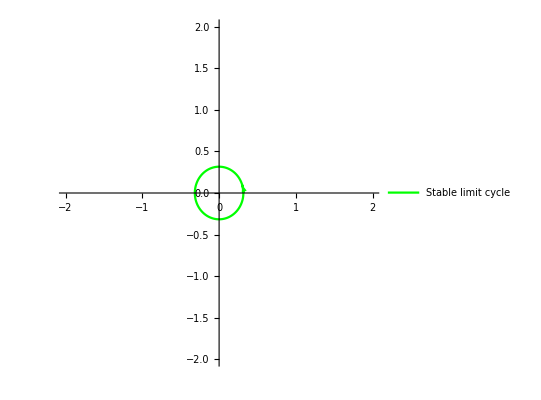

```mathematica
p3 = Show[
ParametricPlot[
Evaluate[{x[t] , y[t]}/. sol2[ r0, 0]]
,{t,0,6} , PlotRange->{{-2,2} , {-2,2}}, PlotStyle->Green, PlotLegends->{" Stable limit cycle "}]]/. Line[x_] :> {Arrowheads[{0.03,0.0,0.03,0.0,0.03,0.0}], Arrow[x]}
```

Everything combined:

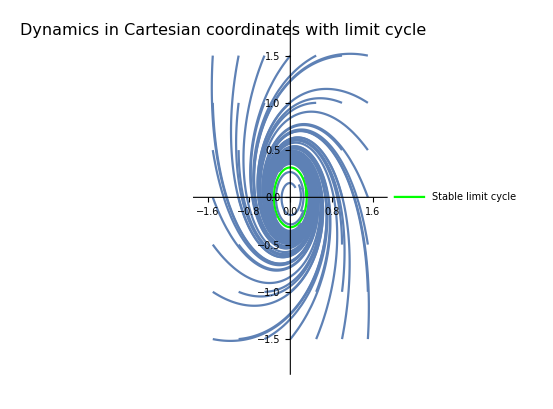

```mathematica
Show[p2,p3,p4, Epilog->Text[Style["Dynamics in Cartesian coordinates with limit cycle",{Black,16}],Offset[{30,-10},Scaled[{0,1}]],{-1,0}]]
```

#### c)

We compare the derivatives

```mathematica
x1' = (μ*r-r^3)*Cos[θ]-r*Sin[θ]*(ω+ν*r^2)
```

(-r^3+r μ) Cos[θ]-r (r^2 ν+ω) Sin[θ]

```mathematica
x2' = (μ*r-r^3)*Sin[θ]+r*Cos[θ]*(ω+ν*r^2)
```

r (r^2 ν+ω) Cos[θ]+(-r^3+r μ) Sin[θ]

Convert derivatives to (x1,x2) coordinates:

```mathematica
FullSimplify[x1'/. {r->Sqrt[x1^2+x2^2], θ->ArcTan[x2/x1]}, Assumptions->Element[x1,Reals]]
```

-(x1^3+x1 x2^2-x1 μ+x1^2 x2 ν+x2^3 ν+x2 ω)/Sign[x1]

```mathematica
FullSimplify[x2'/. {r->Sqrt[x1^2+x2^2], θ->ArcTan[x2/x1]}, Assumptions->Element[x1,Reals]]
```

(-x1^2 x2-x2^3+x2 μ+x1^3 ν+x1 (x2^2 ν+ω))/Sign[x1]

So by comparing, we see that μ = 1/10, ω = 1 and ν = 1

#### d)

```mathematica
T = 2π/(1+1/10) (* period limit cycle; see part a) *)
```

(20 π)/11

```mathematica
soleq[x0_ , y0_] :=NDSolve[
{x'[t]== x[t]/10-y[t]^3-x[t]*y[t]^2-x[t]^2*y[t]-y[t]-x[t]^3, 
y'[t] == x[t]+y[t]/10+x[t]*y[t]^2+x[t]^3-y[t]^3-x[t]^2*y[t], x[0] == x0 , y[0] == y0} 
, {x,y} , {t,0,T}]
```

```mathematica
sold = Evaluate[{x[t] , y[t]}/. soleq[ r0, 0]];
```

```mathematica
x1 = sold[[1,1]];
```

```mathematica
x2 = sold[[1,2]];
```

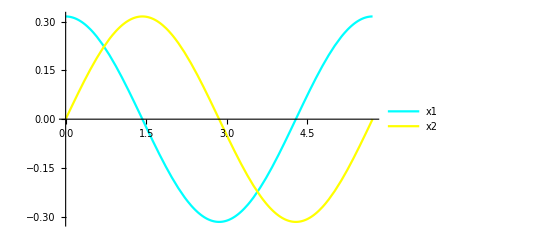

```mathematica
plotx = Plot[{x1,x2},{t,0.,T}, PlotLegends->{"x1","x2"}, PlotStyle->{Cyan, Yellow}]
```

We show that the pair (x1,x2) indeed represents the limit cycle:

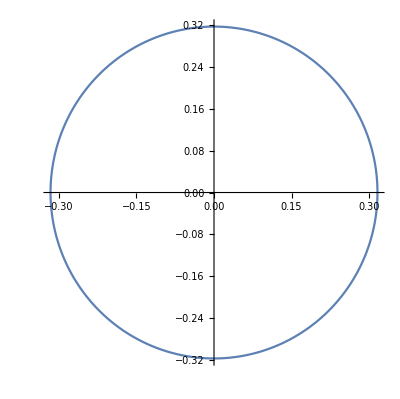

```mathematica
ParametricPlot[{x1,x2}, {t,0,T}]
```

The Jaccobian in Cartesian coordinate equals:

```mathematica
J = {{1/10-x2^2-2*x1*x2-3*x1^2, -3*x2^2-2*x1*x2-x1^2-1}, {1+x2^2+3*x1^2-2*x1*x2, 1/10+2*x1*x2-3*x2^2-x1^2}};
```

We now follow the recipe in the lecture notes to calculate the M matrix in time

```mathematica
M0={{1,0},{0,1}};
funcs=Array[M[#1,#2][t]&,{2,2}];
equations=Flatten@Join[Thread[D[funcs,t]==J.funcs],Thread[funcs==M0/. t->0]];
sM=NDSolveValue[equations,funcs,{t,0,T}];
M11 = sM[[1,1]];
M12 = sM[[1,2]];
M21 = sM[[2,1]];
M22 = sM[[2,2]];
plotm = Plot[{M11,M12,M21,M22},{t,0,T}, PlotLegends->{"M11", "M12", "M21", "M22"}, PlotStyle->{Green,Red,Blue, Black}];
```

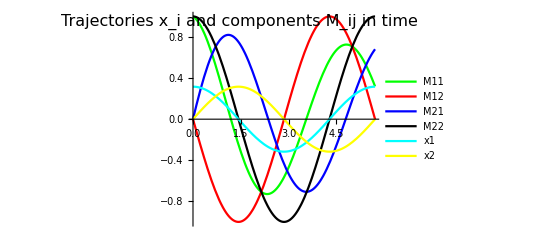

```mathematica
Show[plotm,plotx,Epilog->Text[Style["Trajectories x_i and components M_ij in time",{Black,16}],Offset[{50,-10},Scaled[{0,1}]],{-1,0}] ]
```

#### e)

The values of the M matrix elements at t = T are given by:

```mathematica
M11/.t->T
```

0.319054

```mathematica
M12/.t->T
```

5.5223×10^-7

```mathematica
(* ≈ 0 *)
```

```mathematica
M21/.t->T
```

0.680946

```mathematica
M22/.t->T
```

1.

#### f)

The M matrix at time t = T

```mathematica
MT = {{M11/.t->T,M12/.t->T},{M21/.t->T,M22/.t->T}}
```

{{0.319054,5.5223×10^-7},{0.680946,1.}}

The stability exponents are then:

```mathematica
Log[Eigenvalues[MT]]/T
```

{1.9989×10^-7,-0.2}

```mathematica
(* ≈ {0,-0.2} *)
```

#### g)

For this exercise, we follow section 10.6 in the lecture notes and the explanation of the TA during the exercise session. We start by calculating the Jaccobian in polar coordinates (μ = 1/10, ω = 1 and ν = 1 is assumed here; see part c) ):

```mathematica
μ = 1/10;
ω = 1;
ν = 1;
```

```mathematica
r0 = Sqrt[μ];
```

```mathematica
Jp = {{μ-3*r0^2,0},{2*ν*r0,0}}
```

{{-1/5,0},{√(2/5),0}}

The Jaccobian is a constant matrix, so that the equation for M (in polar coordinates) can be solved using the matrix exponential (we look for M(T)):

```mathematica
Mp = MatrixExp[Jp*T]
```

{{ⅇ^(-4 π/11),0},{√10 ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)),1}}

To revert back to Cartesian coordinates, we need to apply the gradient matrix of the coordinate transformation:

```mathematica
G = {{x1/r0/.t->T,x2/r0/.t->T}, {-x2/r0^2/.t->T, x1/r0^2/.t->T}}
```

{{1.,-2.3519×10^-7},{7.43735×10^-7,3.16228}}

The above expression uses the numerical trajectories for x1 and x2. In turns out to be easier to use the analytical result (which roughly agrees with the above expression) :

```mathematica
G = {{1,0},{0,1/r0}}
```

{{1,0},{0,√10}}

So the matrix in Cartesian coordinates becomes:

```mathematica
MC = Inverse[G].Mp.G
```

{{ⅇ^(-4 π/11),0},{ⅇ^(-4 π/11) (-1+ⅇ^(4 π/11)),1}}

With stability exponents given by:

```mathematica
1/T*Log[Eigenvalues[MC]]
```

{0,-1/5}